```mathematica
SetDirectory[NotebookDirectory[]];
dichotomy ="dichotomy.dat";
golden = "golden.dat";
Results={Flatten@Import[dichotomy], Flatten@Import[golden]} ;
```

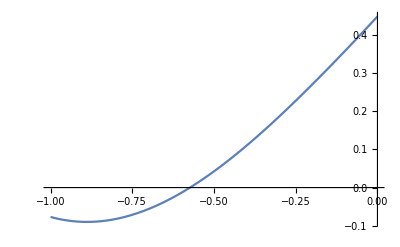

```mathematica
(*Вариант 20*)
R1[x_]:=Sin[(Sqrt[13]*x^3-9*x-5-Sqrt[17])/10];
R2[x_]:=Tan[(x^2+x+2^(1/3))/(3*x-5)];
Plot[-R1[x]-R2[x]-0.6, {x, -1, 0}]
```

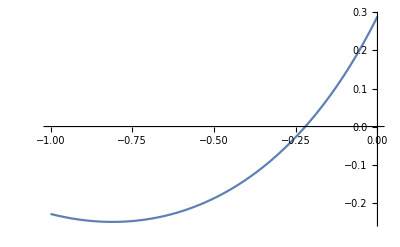

```mathematica
(*Вариант 23*)
R3[x_]:=Sin[(-2*x^2-Sqrt[10]*x+1)/4];
R4[x_]:=((x^2+(√2+√7)*x+1-√5)/(√7*x-√5))^(Log[2]);
Plot[-R3[x]-R4[x]+1.2, {x, -1, 0}]
```

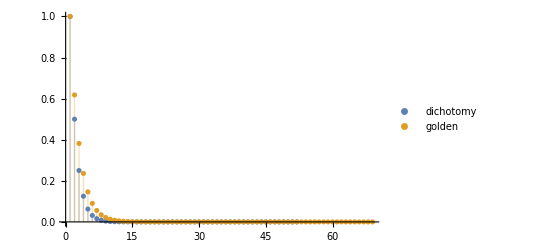

```mathematica
ListPlot[Results, PlotLegends->{"dichotomy", "golden"}, PlotRange->All, Filling->Axis]
```

```mathematica
Len = Min[Length[Results[[1]]],Length[Results[[2]]]];
```

```mathematica
X = Table[Abs[Results[[1,i]]-Results[[2,i]]],{i,1,Len}];
```

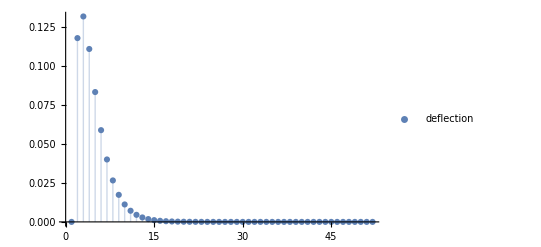

```mathematica
ListPlot[X, PlotLegends->{"deflection"}, PlotRange->All, Filling->Axis]
```